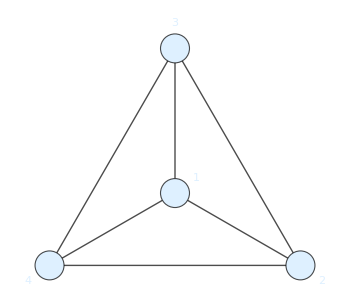

```mathematica
CompleteGraph[4,VertexStyle->LightBlue,VertexSize->Medium,EdgeStyle->Black,ImageSize->350]
```

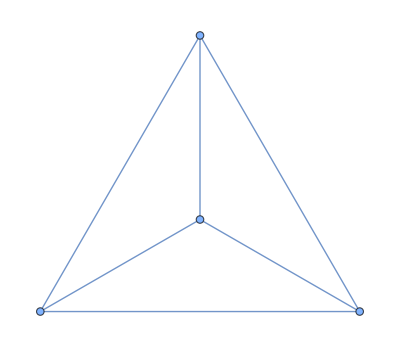
ChromaticNumber[-Graphics-]

```mathematica
ChromaticNumber[CompleteGraph[4]]
```

```mathematica
ChromaticPolynomial[CompleteGraph[4],k]
```

-6 k+11 k^2-6 k^3+k^4

```mathematica
ChromaticIndex[CompleteGraph[4]]
```

ChromaticIndex[-Graphics-]

```mathematica
PlanarGraphQ[CompleteGraph[4]]
```

True

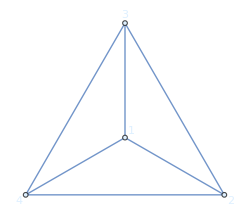
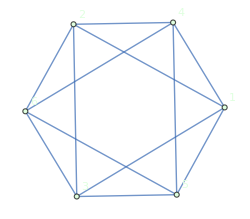

```mathematica
g=CompleteGraph[4];
lg=LineGraph[g];
Row[{Graph[g,VertexLabels->"Name",VertexStyle->LightBlue,ImageSize->250],Graph[lg,VertexLabels->"Name",VertexStyle->LightGreen,ImageSize->250]}]
```

ChromaticIndex[-Graphics-]

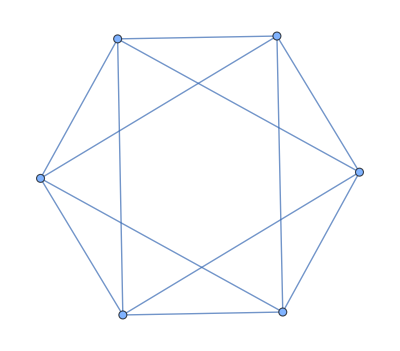
ChromaticIndex[-Graphics-]

ChromaticIndex[-Graphics-]==ChromaticIndex[-Graphics-]

```mathematica
ChromaticIndex[g]

ChromaticIndex[lg]

(*Сравнение*)
ChromaticIndex[g]==ChromaticIndex[lg]
```

```mathematica
s=CompleteGraph[4]
g=s;
FindEdgeColoring[g,ColorData[106,"ColorList"]]
```

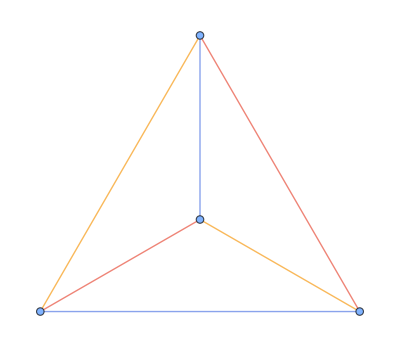

```mathematica
Annotate[g,{EdgeStyle->Thread[EdgeList[g]->%]}]
```

```mathematica
FindVertexColoring[s,ColorData[106,"ColorList"]]
```

```mathematica
FindVertexColoring[s,{RGBColor[0.34398, 0.49112, 0.89936],RGBColor[0.97, 0.606, 0.081],RGBColor[0.91, 0.318, 0.243],RGBColor[0.448, 0.69232, 0.1538],RGBColor[0.62168, 0.2798, 0.6914],RGBColor[0.09096, 0.6296, 0.85532],RGBColor[0.46056, 0.40064, 0.81392],RGBColor[0.94, 0.462, 0.162],RGBColor[0., 0.7, 0.7],RGBColor[0.827051, 0.418034, 0.0243459],RGBColor[0.5511749434976025, 0.32014794962639853, 0.8720626412559938],RGBColor[0.72694101250947, 0.7196601125010522, 0.],RGBColor[0.8680706456216862, 0.2563858708756628, 0.30321559063052295],RGBColor[0.2418693812442152, 0.5065044950046278, 0.9902432574930582],RGBColor[0.9573908706237908, 0.5369543531189542, 0.11504464931576472]}]
```

{RGBColor[0.34398, 0.49112, 0.89936],RGBColor[0.97, 0.606, 0.081],RGBColor[0.91, 0.318, 0.243],RGBColor[0.448, 0.69232, 0.1538]}

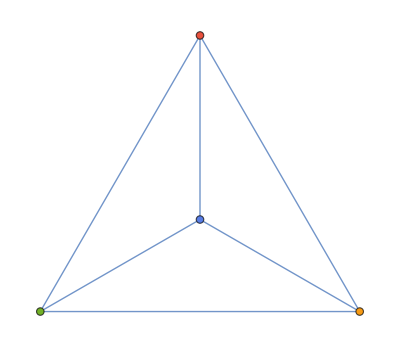

```mathematica
Annotate[s,{VertexStyle->Thread[VertexList[s]->%]}]
```

```mathematica
VertexCoverQ[s,{1,3}]
```

False

```mathematica
FindVertexCover[s]
```

{1,2,3}